# Parse Complete Info

```mathematica
SetDirectory["/Users/zhuohuizhang/Dropbox/IsraelCases"]
```

/Users/zhuohuizhang/Dropbox/IsraelCases

## Data

### Geographical Data

#### List of Destinations from Ben Gurion Airport

```mathematica
DestinationsTLV=Association[{"אוסטריה"->Entity["Country","Austria"],"זלצבורג"->Entity["City",{"Salzburg","Salzburg","Austria"}], "אזרבייג'ן"->Entity["Country","Azerbaijan"],"אזרבייג׳ן"->Entity["Country","Azerbaijan"],"באקו"->Entity["City",{"Baku","Baki","Azerbaijan"}],"וינה"->Entity["City",{"Vienna","Vienna","Austria"}],"ארמניה"->Entity["Country","Armenia"],"ירוואן"->Entity["City",{"Yerevan","Yerevan","Armenia"}],"בלגיה"->Entity["Country","Belgium"],"בריסל"->Entity["City",{"Brussels","Brussels","Belgium"}],"ברזיל"->Entity["Country","Brazil"],"סאו פאולו"->Entity["City",{"SaoPaulo","SaoPaulo","Brazil"}],"בולגריה"->Entity["Country","Bulgaria"],"סופיה"->Entity["City",{"Sofia","SofijaGrad","Bulgaria"}],"ורנה"->Entity["City",{"Varna","Varna","Bulgaria"}],"קנדה"->Entity["Country","Canada"],"מונטריאול"->Entity["City",{"Montreal","Quebec","Canada"}],"טורונטו"->Entity["City",{"Toronto","Ontario","Canada"}],"צ'ילה"-> Entity["Country","Chile"],"צ׳ילה"-> Entity["Country","Chile"],"סנטיאגו דה צ'ילה"->Entity["City",{"Santiago","Metropolitana","Chile"}],"סנטיאגו דה צ׳ילה"->Entity["City",{"Santiago","Metropolitana","Chile"}],"סין"->Entity["Country","China"],"בייג'ינג"->Entity["City",{"Beijing","Beijing","China"}],"בייג׳ינג"->Entity["City",{"Beijing","Beijing","China"}],"שנזן"->Entity["City",{"Shenzhen","Guangdong","China"}],"גואנגזו"->Entity["City",{"Guangzhou","Guangdong","China"}],"הונג קונג"->Entity["City",{"HongKong","HongKong","HongKong"}],"שנחאי"->Entity["City",{"Shanghai","Shanghai","China"}],"צ'נגדו"->Entity["City",{"Chengdu","Sichuan","China"}],"צ׳נגדו"->Entity["City",{"Chengdu","Sichuan","China"}],"קפריסין"->Entity["Country","Cyprus"],"לרנקה"->Entity["City",{"Larnaca","Larnaca","Cyprus"}],"פאפוס"->Entity["City",{"Pafos","Paphos","Cyprus"}],"צ'כיה"->Entity["Language","Czech::4z65s"],"צ׳כיה"->Entity["Language","Czech::4z65s"],"פראג"->Entity["City",{"Prague","Prague","CzechRepublic"}],"דנמרק"->Entity["Country","Denmark"],"קופנהגן"->Entity["City",{"Copenhagen","Copenhagen","Denmark"}],"פינלנד"->Entity["Country","Finland"],"הלסינקי"->Entity["City",{"Helsinki","Uusimaa","Finland"}],"צרפת"->Entity["Country","France"],"פריז"->Entity["City",{"Paris","IleDeFrance","France"}],"ליון"->Entity["City",{"Lyon","RhoneAlpes","France"}],"בורדו"-> Entity["City",{"Bordeaux","Aquitaine","France"}],"מרסיי"->Entity["City",{"Marseille","ProvenceAlpesCoteDAzur","France"}],"נאנט"->Entity["City",{"Nantes","PaysDeLaLoire","France"}],"ניס"->Entity["City",{"Nice","ProvenceAlpesCoteDAzur","France"}],"טולוז"->Entity["City",{"Toulouse","MidiPyrenees","France"}],"גרמניה"->Entity["Country","Germany"],"באדן"->Entity["City",{"BadenBaden","BadenWurttemberg","Germany"}],"פרנקפורט"->Entity["City",{"Frankfurt","Hesse","Germany"}],"ממינגן"->Entity["Airport","EDJA"],"מינכן"->Entity["City",{"Munich","Bavaria","Germany"}],"שטוטגרט"->Entity["City",{"Stuttgart","BadenWurttemberg","Germany"}],"יוון"->Entity["Country","Greece"],"אתונה"->Entity["City",{"Athens","Attiki","Greece"}],"סלוניקי"->Entity["City",{"Thessaloniki","Thessaloniki","Greece"}],"הונגריה"->Entity["Country","Hungary"],"בודפשט"->Entity["City",{"Budapest","Budapest","Hungary"}],"דברצן"->Entity["City",{"Debrecen","HajduBihar","Hungary"}],"הודו"-> Entity["Country","India"],"מומבאי"->Entity["City",{"Bombay","Maharashtra","India"}],"ניו דלהי"->Entity["City",{"NewDelhi","Delhi","India"}],"גואה"->Entity["AdministrativeDivision",{"Goa","India"}],"איטליה"->Entity["Country","Italy"],"בולוניה"->Entity["City",{"Bologna","EmiliaRomagna","Italy"}],"רומא"->Entity["City",{"Rome","Lazio","Italy"}],"מילאנו"->Entity["City",{"Milan","Lombardy","Italy"}],"פירנצה"->Entity["City",{"Florence","Toscana","Italy"}],"נאפולי"->Entity["City",{"Naples","Campania","Italy"}],"ונציה"->Entity["City",{"Venice","Veneto","Italy"}],"ורונה"->Entity["City",{"Verona","Veneto","Italy"}],"יפן"->Entity["Country","Japan"],"טוקיו"->Entity["City",{"Tokyo","Tokyo","Japan"}],"לטביה"->Entity["Country","Latvia"],"ריגה"->Entity["City",{"Riga","Riga","Latvia"}],"ליטא"->Entity["Country","Lithuania"],"קובנה"->Entity["City",{"Kaunas","Kauno","Lithuania"}],"וילנה"->Entity["City",{"Vilnius","Vilniaus","Lithuania"}],"הולנד"->Entity["Country","Netherlands"],"אמסטרדם"->Entity["City",{"Amsterdam","NoordHolland","Netherlands"}],"איינדהובן"->Entity["City",{"Eindhoven","NoordBrabant","Netherlands"}],"נורווגיה"->Entity["Country","Norway"],"אוסלו"->Entity["City",{"Oslo","Oslo","Norway"}],"פולין"->Entity["Country","Poland"],"גדנסק"->Entity["City",{"Gdansk","Pomorskie","Poland"}],"קטוביץ"->Entity["City",{"Katowice","Slaskie","Poland"}],"קרקוב"->Entity["City",{"Krakow","Malopolskie","Poland"}],"לובלין"->Entity["City",{"Lublin","Lubelskie","Poland"}],"פוזנן"->Entity["City",{"Poznan","Wielkopolskie","Poland"}],"ורשה"->Entity["City",{"Warsaw","Mazowieckie","Poland"}],"ורוצלב"->Entity["City",{"Wroclaw","Dolnoslaskie","Poland"}],"פורטוגל"->Entity["Country","Portugal"],"ליסבון"->Entity["City",{"Lisbon","Lisboa","Portugal"}],"רומניה"->Entity["Country","Romania"],"בוקרשט"->Entity["City",{"Bucharest","Bucharest","Romania"}],"יאסי"->Entity["City",{"Iasi","Iasi","Romania"}],"סיביו"->Entity["City",{"Sibiu","Sibiu","Romania"}],"טימישוארה"->Entity["City",{"Timisoara","Timis","Romania"}],"רואנדה"->Entity["Country","Rwanda"],"קיגאלי"->Entity["City",{"Kigali","KigaliCity","Rwanda"}],"סיישל"->Entity["Country","Seychelles"],"סלובקיה"->Entity["Country","Slovakia"],"ברטיסלבה"->Entity["City",{"Bratislava","Bratislavsky","Slovakia"}],"דרום אפריקה"->Entity["Country","SouthAfrica"],"יוהנסבורג"->Entity["City",{"Johannesburg","Gauteng","SouthAfrica"}],"ספרד"->Entity["Country","Spain"],"ברצלונה"->Entity["City",{"Barcelona","Barcelona","Spain"}],"מדריד"->Entity["City",{"Madrid","Madrid","Spain"}],"טנריף"->Entity["Island","Tenerife"],"מלאגה"->Entity["City",{"Malaga","Malaga","Spain"}],"אינסברוק"->Entity["City",{"Innsbruck","Tirol","Austria"}], "שבדיה"->Entity["Country","Sweden"],"שטוקהולם"->Entity["City",{"Stockholm","Stockholm","Sweden"}],"שוויץ"->Entity["Country","Switzerland"],"ז'נבה"->Entity["City",{"Geneva","Geneva","Switzerland"}],"ז׳נבה"->Entity["City",{"Geneva","Geneva","Switzerland"}],"באזל"->Entity["City",{"Basel","BaselTown","Switzerland"}],"ציריך"->Entity["City",{"Zurich","Zurich","Switzerland"}],"תאילנד"->Entity["Country","Thailand"],"בנגקוק"->Entity["City",{"Bangkok","Bangkok","Thailand"}],"טורקיה"->Entity["Country","Turkey"],"איסטנבול"->Entity["City",{"Istanbul","Istanbul","Turkey"}],"איזמיר"->Entity["City",{"Izmir","Izmir","Turkey"}],"אוקראינה"->Entity["Country","Ukraine"],"אודסה"->Entity["City",{"Odesa","Odesa","Ukraine"}],"הממלכה המאוחדת"->Entity["Country","UnitedKingdom"],"האו”ם"-> Entity["Country","UnitedKingdom"],"האו\"ם"-> Entity["Country","UnitedKingdom"],"אדינבורו"->Entity["City",{"Edinburgh","Edinburgh","UnitedKingdom"}],"לונדון"->Entity["City",{"London","GreaterLondon","UnitedKingdom"}],"מנצ'סטר"->Entity["City",{"Manchester","Manchester","UnitedKingdom"}],"מנצ׳סטר"->Entity["City",{"Manchester","Manchester","UnitedKingdom"}],"ארה\"ב"-> Entity["Country","UnitedStates"],"ארה”ב"-> Entity["Country","UnitedStates"],"בוסטון"->Entity["City",{"Boston","Massachusetts","UnitedStates"}],"שיקגו"->Entity["City",{"Chicago","Illinois","UnitedStates"}],"לוס אנג'לס"->Entity["City",{"LosAngeles","California","UnitedStates"}],"לוס אנג׳לס"->Entity["City",{"LosAngeles","California","UnitedStates"}],"מיאמי"->Entity["City",{"Miami","Florida","UnitedStates"}],"ניו יורק"->Entity["City",{"NewYork","NewYork","UnitedStates"}],"סן פרנסיסקו"->Entity["City",{"SanFrancisco","California","UnitedStates"}],"וושינגטון"->Entity["City",{"Washington","DistrictOfColumbia","UnitedStates"}],"לאס וגאס"->Entity["City",{"LasVegas","Nevada","UnitedStates"}],"אורלנדו"->Entity["City",{"Orlando","Florida","UnitedStates"}],"תל אביב"->Entity["City",{"TelAvivYafo","TelAviv","Israel"}],"ישראל"->Entity["Country","Israel"] ,"נתב”ג"->Entity["City",{"TelAvivYafo","TelAviv","Israel"}],"נתב\"ג"->Entity["City",{"TelAvivYafo","TelAviv","Israel"}],"ת\"א"->Entity["City",{"TelAvivYafo","TelAviv","Israel"}]}];
```

WolframAlphaQueryParseResults

Israel

#### List of Israel Municipalities

```mathematica
rawmuni=Import["IsraelMunicipalities.xlsx","XLSX"];
```

```mathematica
AmbiguousCharacters1={"\"","”"};
AmbiguousCharacters2={"'","'","׳","’"};
AmbiguousCharacters3={"-"};
```

```mathematica
CreateStringPolymorphism[rule_]:=Module[{allchar1,allchar2,allchar3},
allchar1=StringCases[rule⟦1⟧,AmbiguousCharacters1];
allchar2=StringCases[rule⟦1⟧,AmbiguousCharacters2];
allchar3=StringCases[rule⟦1⟧,AmbiguousCharacters3];]
```

```mathematica
IsraelMunicipalitiesHebToEngWolfram=Association[(#⟦1⟧->#⟦2⟧&/@Join[Select[rawmuni[[1]],#[[3]]==1&],Select[rawmuni[[2]],#[[3]]==1&],Select[rawmuni[[3]],#[[3]]==1&],Select[rawmuni[[4]],#[[3]]==1&]]⟦All,1;;2⟧)//DeleteDuplicates];
```

```mathematica
IsraelMunicipalitiesHebToEng=Association[(#⟦1⟧->#⟦2⟧&/@Join[rawmuni[[1]],rawmuni[[2]],rawmuni[[3]],rawmuni[[4]]]⟦All,1;;2⟧)//DeleteDuplicates];
```

```mathematica
IsraelMunicipalitiesHebrew=Keys[IsraelMunicipalitiesHebToEng];
```

#### Wolfram List of Cities

```mathematica
WolframNamesIsraeliCities={"Abu Ghosh","Adi","Afula","Akko","al-Burj","al-Jalamah","al-Judayrah","Arad","Arara-BaNegev","Arara","Arrabe","Ashdod","Ashqelon","Atlit","Aydah","Azur","Baqa-Jatt","Basma","Basmat Tabun","Bat Hefer","Bat Yam","Beer Sheva","Beer Yaaqov","Beit Jann","Bene Ayish","Bene Beraq","Bet Dagan","Bet Shean","Bet Shemesh","Bet Yizhaq","Binyamina-Givat Ada","Bir El-Maksur","Bueine-Nujeidat","Buqata","Dabburiyya","Daliyat Al Karmel-Isifya","Deir Hanna","Dimona","Eilabun","Ein Mahel","Ein Naqquba","Elad","Elat","Elyakhin","Even Yehuda","Fassuta","Fureidis","Gan Ner","Ganne Tiqwa","Gan Yavne","Gedera","Givat Avni","Givatayim","Givat Ela","Givat Shemuel","Glil Yam","Hadera","Haifa","Hazor HaGelilit","Herzeliyya","Hod HaSharon","Holon","Hura","Hurfeish","Ibillin","Ibtin","Iksal","Ilut","Ir Hahamisha","Jaffa","Jaljulye","Jerusalem","Jish","Jisr Az-Zarqa","Judeide-Maker","Kaabiyye-Tabbash-Hajaj","Kabul","Kafar Bara","Kafar Kama","Kafar Kanna","Kafar Manda","Kafar Misr","Kafar Qara","Kafar Qasem","Kafar Yasif","Kaokab Abu Al-Hija","Karme Yosef","Karmiel","Kefar Habad","Kefar Sava","Kefar Shemaryahu","Kfar Tavor","Kefar Weradim","Kefar Yona","Kisra-Sumei","Kokhav Yair","Kuseife","Lappid","Laqye","Lehavim","Lod","Maale Iron","Maalot-Tarshiha","Majdal Shams","Masade","Mashhed","Mattan","Mazkeret Batya","Mazraa","Merkaz Shappira","Metar","Mevasserat Ziyyon","Mielya","Migdal HaEmeq","Mizpe Ramon","Modiin-Makkabim-Reut","Mugar","Muqeible","Nahariyya","Nahef","Naura","Nazerat Illit","Nazerat","Nehalim","Nein","Nesher","Nes Ziyyona","Netanya","Netivot","Nof Ayyalon","Nofit","Nordiyya","Ofaqim","Omer","Oranit","Or Aqiva","Or Yehuda","Pardes Hanna-Karkur","Pardesiyya","Peqiin","Petah Tiqwa","Qalansawe","QaTannah","Qazir-Harish","Qazrin","Caesarea","Qiryat Atta","Qiryat Bialik","Qiryat Eqron","Qiryat Gat","Qiryat Malakhi","Qiryat Motzkin","Qiryat Ono","Qiryat Shemona","Qiryat Tivon","Qiryat Yam","Qiryat Yearim","Raanana","Rahat","Ramat Efal","Ramat Gan","Ramat HaSharon","Ramat Yishay","Rame","Ramla","Rehovot","Reine","Rekhasim","Rishon LeZiyyon","Rosh HaAyin","Rosh Pinna","Rumat Heib","Sajur","Sakhnin","Sallama","Savyon","Sederot","Segev-Shalom","Shaab","Shagor","Shefaram","Sheikh Dannun","Shibli-Umm Al-Ghanam","Shoham","Sulam","Tamra","Tayibe","Tel Aviv","Tel Mond","Tel Sheva","Tiberias","Timrat","Tirat Karmel","Tirat Zvi","Tire","Tuba-Zangariyye","Turan","Umm Al-Fahm","Uzeir","Yafi","Yavneel","Yavne","Yehud","Yehud-Newe Efrayim","Yeroham","Yoqneam Illit","Zarzir","Zefat","Zemer","Zikhron Ya'akov","Zikhron Yaaqov","Zoran-Qadima","Zububa","Zur Hadassa"};
WolframWestBankCities={"Abu Dis","Abud","Abwein","ad-Duhaysah","Ajjah","al-Amarri","al-Araqah","al-Arrub","al-Awja","al-Ayzariyah","al-Birah","al-Fandaqumiyah","al-Farah","al-Fawwar","Alfe Menashe","al-Hadr","al-Jalazun","al-Jib","al-Jiftlik","al-Judaydah","al-Judayrah","al-Karmil","Allon Shevut","al-Lubban as-Sarqiyah","al-Mazraah as-Sarqiyah","al-Mugayyir","al-Mugayyir","al-Qubaybah","al-Ubaydiyah","al-Yamun","Al-Zaitounah","Anabta","Anata","Anin","Anzah","Aqbah Jabbar","Aqqaba","Aqraba","Ariel","Ariha","Arrabah","ar-Ram","Arranah","ar-Rihiyah","ArTas","Arurah","Asirah al-Qibliyah","Asirah as-Samaliyah","Askar","as-Samu","as-Sawiyah","as-Suyuh","ATarah","aT-Taybah","aT-Taybah","Attil","Awarta","Aydah","Aynabus","Ayn Yabrud","AzmuT","az-Zababidah","az-Zahiriyah","az-Zawiyah","Azzun","Balata al-Balad","BalaTah","Bala","Bani Naim","Baqah as-Sarqiyah","BarTaah as-Sarqiyah","Battir","Bayta","Bayt Awwa","Bayt Dajan","Bayt Fajjar","Bayt Furik","Bayt Iba","Baytillu","Bayt Imrin","Bayt Jala","Bayt Kahil","Bayt Lahm","Bayt Lid","Bayt Liqya","Bayt Sahur","Bayt Sira","Bayt Surik","Bayt Ula","Bayt Ummar","Baytuniya","Bayt Ur at-Tahta","Betar Illit","Bet Arye","Bet El","Biddu","Biddya","Bir Nabala","Birqin","Bir Zayt","Bitin","Bizzariya","Bruqin","Burin","Burqah","Burqah","Dayr Abu Daif","Dayr Abu Masal","Dayr al-Gusun","Dayr al-HaTab","Dayr Ammar","Dayr as-Saraf","Dayr as-Sudan","Dayr BalluT","Dayr Dibwan","Dayr Istiya","Dayr Jarir","Dayr Samit","Dhinnabah","Duma","Dura al-Qar","Dura","Efrata","Ein Qiniyye","Eli","Elqana","Fahmah","Faqquah","Farun","Geva Binyamin","Givat Zeev","Hablah","Hajjah","Halhul","Har Adar","Haras","Harbata al-Misbah","Haris","Hashmonaim","Hebron","Hirbat Abu Falah","Hizma","Kharsa","Husan","Huwwara","Idhna","Iktaba","Illar","Immanuel","Immatin","Jaba","Jaba","Jalbun","Jammain","Janin","Jayyus","JinsafuT","Jit","Kafr ad-Dik","Kafr al-Labad","Kafr Aqab","Kafr Dan","Kafr Jammal","Kafr Malik","Kafr Nimah","Kafr Qaddum","Kafr Qallil","Kafr Rai","Kafr Tult","Kawbar","Kefar Adummim","Kifl Haris","Kokhav Yaaqov","Kufayrit","Lappid","Maale Adummim","Majdal Bani Fadil","Mardah","Maytalun","Mazari an-Nubari","Misliyah","Modiin Illit","Modiin-Makkabim-Reut","Muhayyam Dayr Ammar","Muhayyam Janin","Muhayyam Qalandiya","Muhayyam Tulkarm","Nablus","Nahhalin","Nazlat Isa","Nilin","Nuba","Nur Sams","Ofra","Qabalan","QabaTiyah","Qaffin","Qalqilyah","Qarawat Bani Hassan","Qarawat Bani Zayd","Qarne Shomeron","Qaryut","QaTannah","Qedummim","Qibya","Qiryat Arba","Qusrah","Raba","Rafat","Rafat","Ram Allah","Ramin","Rammun","Rantis","Rujayb","Rummanah","SabasTiyah","Saffa","Sair","Salfit","Salim","Sanniriya","Sanur","Sarrah","SarTah","Sayda","Shaare Tiqwa","Shilo","Silat al-Haritiyah","Silat az-Zahr","Silwad","Sinjil","Siris","Suqba","Surif","Taffuh","Talfit","Tall as-SulTan","Tall","Talluzah","Talmon","Tammun","Tarqumiya","Tayasir","Tubas","Tulkarm","Tuqu","Turmusayya","Urif","Yabad","Yasid","Yatma","YaTTa","Zatarah","Zayta"};
```

#### Comparison

```mathematica
StringJoin[#<>"\n"&/@Complement[Join[WolframNamesIsraeliCities,WolframWestBankCities],Intersection[Values[IsraelMunicipalitiesHebToEng],Join[WolframNamesIsraeliCities,WolframWestBankCities]]]]//Print
```

Abud
Abu Dis
Abwein
ad-Duhaysah
Ajjah
Allon Shevut
Al-Zaitounah
al-Amarri
al-Araqah
al-Arrub
al-Awja
al-Ayzariyah
al-Birah
al-Burj
al-Fandaqumiyah
al-Farah
al-Fawwar
al-Hadr
al-Jalamah
al-Jalazun
al-Jib
al-Jiftlik
al-Judaydah
al-Judayrah
al-Karmil
al-Lubban as-Sarqiyah
al-Mazraah as-Sarqiyah
al-Mugayyir
al-Qubaybah
al-Ubaydiyah
al-Yamun
Anabta
Anata
Anin
Anzah
Aqbah Jabbar
Aqqaba
Aqraba
Arara-BaNegev
Arrabah
Arranah
ArTas
Arurah
ar-Ram
ar-Rihiyah
Asirah al-Qibliyah
Asirah as-Samaliyah
Askar
as-Samu
as-Sawiyah
as-Suyuh
ATarah
Attil
aT-Taybah
Awarta
Aynabus
Ayn Yabrud
AzmuT
Azzun
az-Zababidah
az-Zahiriyah
az-Zawiyah
Bala
Balata al-Balad
BalaTah
Bani Naim
Baqah as-Sarqiyah
Baqa-Jatt
BarTaah as-Sarqiyah
Battir
Bayta
Bayt Awwa
Bayt Dajan
Bayt Fajjar
Bayt Furik
Bayt Iba
Baytillu
Bayt Imrin
Bayt Kahil
Bayt Lid
Bayt Liqya
Bayt Sahur
Bayt Sira
Bayt Surik
Bayt Ula
Bayt Ummar
Baytuniya
Bayt Ur at-Tahta
Bet El
Biddu
Biddya
Binyamina-Givat Ada
Bir El-Maksur
Bir Nabala
Birqin
Bir Zayt
Bitin
Bizzariya
Bruqin
Bueine-Nujeidat
Burin
Burqah
Daliyat Al Karmel-Isifya
Dayr Abu Daif
Dayr Abu Masal
Dayr al-Gusun
Dayr al-HaTab
Dayr Ammar
Dayr as-Saraf
Dayr as-Sudan
Dayr BalluT
Dayr Dibwan
Dayr Istiya
Dayr Jarir
Dayr Samit
Dhinnabah
Duma
Dura
Dura al-Qar
Ein Qiniyye
Fahmah
Faqquah
Farun
Hablah
Hajjah
Halhul
Haras
Harbata al-Misbah
Haris
Hirbat Abu Falah
Hizma
Husan
Huwwara
Idhna
Iktaba
Illar
Immatin
Jaba
Jalbun
Jammain
Jayyus
JinsafuT
Jisr Az-Zarqa
Jit
Judeide-Maker
Kaabiyye-Tabbash-Hajaj
Kafr ad-Dik
Kafr al-Labad
Kafr Aqab
Kafr Dan
Kafr Jammal
Kafr Malik
Kafr Nimah
Kafr Qaddum
Kafr Qallil
Kafr Rai
Kafr Tult
Kaokab Abu Al-Hija
Kawbar
Kharsa
Kifl Haris
Kisra-Sumei
Kokhav Yaaqov
Kufayrit
Maale Adummim
Maalot-Tarshiha
Majdal Bani Fadil
Mardah
Maytalun
Mazari an-Nubari
Misliyah
Modiin-Makkabim-Reut
Muhayyam Dayr Ammar
Muhayyam Janin
Muhayyam Qalandiya
Muhayyam Tulkarm
Nahhalin
Nazlat Isa
Nilin
Nuba
Nur Sams
Pardes Hanna-Karkur
Qabalan
QabaTiyah
Qaffin
Qalqilyah
Qarawat Bani Hassan
Qarawat Bani Zayd
Qarne Shomeron
Qaryut
Qazir-Harish
Qibya
Qusrah
Raba
Rafat
Ramin
Rammun
Rantis
Rujayb
Rummanah
SabasTiyah
Saffa
Sair
Salfit
Salim
Sanniriya
Sanur
Sarrah
SarTah
Sayda
Segev-Shalom
Shaare Tiqwa
Shibli-Umm Al-Ghanam
Silat al-Haritiyah
Silat az-Zahr
Silwad
Sinjil
Siris
Suqba
Surif
Taffuh
Talfit
Tall
Tall as-SulTan
Talluzah
Tammun
Tarqumiya
Tayasir
Tubas
Tuba-Zangariyye
Tulkarm
Tuqu
Turmusayya
Umm Al-Fahm
Urif
Yabad
Yasid
Yatma
YaTTa
Yehud
Yehud-Newe Efrayim
Zatarah
Zayta
Zikhron Ya'akov
Zoran-Qadima

```mathematica
IsraelMunicipalitiesHebToEng["ראשל\"צ"]
```

Rishon LeZiyyon

```mathematica
StringContainsQ["ראשל\"צ",AmbiguousCharacters1]
```

True

#### Airline Companies

```mathematica
AirlinesHebToEngWolfram=Association[(#⟦1⟧->#⟦2⟧&/@Join[rawmuni[[5]]]⟦All,1;;2⟧)//DeleteDuplicates];
```

```mathematica
AirlineNames=Keys[AirlinesHebToEngWolfram];
```

#### Train Stations

### Languages

#### Hebrew Language Sentence

```mathematica
HebrewText={"א","ב","ג","ד","ה","ו","ז","ח","ט","י","כ","ך","ל","מ","ם","נ","ן","ס","ע","פ","ף","צ","ץ","ק","ר","ש","ת","\"","׳","'",Whitespace}..;
```

#### Activities

Keywords on activities

```mathematica
TrainKeywords={"רכבת ל"~~IsraelMunicipalitiesHebrew,"לרכבת ","ברכבת ","רכבת מ"~~IsraelMunicipalitiesHebrew,"תחנת רכבת ","מ"~~IsraelMunicipalitiesHebrew~~" ל"~~IsraelMunicipalitiesHebrew,"ל"~~IsraelMunicipalitiesHebrew~~" מ"~~IsraelMunicipalitiesHebrew};
BusKeywords={" קו "~~purenumber};
ShoppingAssociations=Association[{"קניון"->"Mall","חנות"->"Shop","חנויות"->"Shop","אושר עד"->"Osher Ad","שופרסל"-> "Shufersal","רמי לוי"->"Rami Levy","יוחננוף"->"Yochananof","בר כל"->"Bar Kol","בר כול"->"Bar Kol","ברכול"->"Bar Kol","פרש מרקט"->"Fresh Market","פרשמרקט"->"Fresh Market","קשת טעמים"->"Keshet Teamim","סופר יודה"->"Super Yuda","טיב טעם"->"Tiv Taam","ויקטורי"->"Victory","יינות ביתן"->"Yeinot Beitan","סופר-פארם"->"Superpharm","סופרפארם"->"Superpharm","אלונית"->"Alonit","איקאה"-> "IKEA"}];
ShoppingKeywords=Keys[ShoppingAssociations];
ShopNames=ShoppingKeywords⟦4;;All⟧;
BankAssociations={"מזרחי-טפחות"->"Mizrahi Tefahot","מזרחי טפחות"->"Mizrahi Tefahot","בנק הפועלים"->"Bank Hapoalim","בנק לאומי"->"Bank Leumi","דיסקונט"->"Discount Bank"};
BankKeywords=Keys[BankAssociations={"מזרחי-טפחות"->"Mizrahi Tefahot","מזרחי טפחות"->"Mizrahi Tefahot","בנק הפועלים"->"Bank Hapoalim","בנק לאומי"->"Bank Leumi","דיסקונט"->"Discount Bank"}];
SchoolKeywords={"בית ספר","בית הספר","בה\"ס ","בי\"ס ","ביה\"ס ","בה\"ס ","בה”ס ","בי”ס ","ביה”ס ","בה”ס "};
SynagogueKeywords={"בית כנסת","בית הכנסת","בה\"כ","בי\"כ","ביה\"כ","בה\"כ","בה”כ","בי”כ","ביה”כ","בה”כ"};
RestaurantKeywords={"מסעדה ","מסעדת ","קפה ","קפת "," בר "," גריל "};
PlacePrefix[type_]:=Switch[type,
"Street",{"רחוב ","רח׳ ","רח'"," בר","דרך ","שד׳ ","שדרות "},
"Restaurant",{"מסעדה ","מסעדת ","קפה ","קפת ","בבר "," בר "," גריל "},
"Synagogue",{"בית כנסת","בית הכנסת","בה\"כ","בי\"כ","ביה\"כ","בה\"כ","בה”כ","בי”כ","ביה”כ","בה”כ"},
"School",{"בית ספר","בית הספר","בה\"ס","בי\"ס","ביה\"ס","בה\"ס","בה”ס","בי”ס","ביה”ס","בה”ס"},
"Shopping",{"קניון","חנות","חנויות"},
"Hospital",{"בה\"ח","בי\"ח","ביה\"ח","בה\"ח","בה”ח","בי”ח","ביה”ח","בה”ח"}
]
```

### Parsing Placenames

#### Regions

```mathematica
RegionPreliminaryList={"ירושלים","צפון","חיפה","מרכז","תל אביב","תל–אביב","ת”א","ת\"א","דרום","יהודה ושומרון","שרון"};
RegionVariationList={"מחוז"~~" "~~"ה"~~RegionPreliminaryList,"מחוז"~~" "~~RegionPreliminaryList,"אזור"~~" "~~"ה"~~RegionPreliminaryList,"אזור"~~" "~~RegionPreliminaryList,"ה"~~RegionPreliminaryList,"מ"~~RegionPreliminaryList,"ב"~~RegionPreliminaryList~~" "~~"הארץ"};
EnglishRegionRule=Association[{"ירושלים"->"Jerusalem","הצפון"-> "Northern","צפון"-> "Northern","חיפה"-> "Haifa" ,"המרכז"->"Hamerkaz","מרכז"->"Hamerkaz","תל אביב"->"Tel Aviv","תל–אביב"->"Tel Aviv","ת\"א"->"Tel Aviv","ת”א"->"Tel Aviv","הדרום"->"Hadarom","דרום"->"Hadarom","יהודה ושומרון"->"WestBank","שרון"->"Hamerkaz"}];
```

#### Cities

```mathematica
CityPreliminaryList=IsraelMunicipalitiesHebrew;
CityVariationList={CityPreliminaryList,"עיר "~~CityPreliminaryList,"בישוב "~~CityPreliminaryList,"מ"~~CityPreliminaryList,"ל"~~CityPreliminaryList};
```

#### Airport Destinations

```mathematica
DestinationPreliminaryList=Join[Keys[DestinationsTLV],{"ישראל","תל אביב","נתב”ג","נתב\"ג"}]//DeleteDuplicates;
DestinationVariationList={"ל"~~DestinationPreliminaryList," ב"~~DestinationPreliminaryList}//Flatten;
DepartureVariationList={"מ"~~DestinationPreliminaryList}//Flatten;
```

#### Streets, Places and Addresses

```mathematica
PlacenameVariationList={{"רחוב ","רח׳ "}~~HebrewText~~{purenumber,",","."},"צומת "~~___,"קניוון "~~___,"מרכז "~~___,"בית כנסת "~~___,"בית הכנסת "~~___,"בית ספר"~~___,"בית הספר"~~___,"כביש "~~___,"מסעדת "~~___,"חנות "~~___,"מלון "~~___,"מלון "~~___,"סופרמרקט "~~__};
PlacePatterns[type_]:=PlacePrefix[type]~~HebrewText~~Switch[type,
"Street",{purenumber,",","."},
"Restaurant",{".",",","\n",EndOfString," ברחוב","רח'"," רחוב"},
"Synagogue",{".",",","\n",EndOfString," ברחוב","רח'"," רחוב"},
"School",{".",",","\n",EndOfString," ברחוב","רח'"," רחוב"},
"Shopping",{".",",","\n",EndOfString," ברחוב","רח'"," רחוב"}
];
```

### Pattern Matching for Date, Index, Time and Flight

Basic strings, like date, time and index

```mathematica
GetStrDate[str_]:=(StringDelete[#,{"-"}]&)/@StringCases[str,NumberString~~"."~~NumberString]//DeleteDuplicates;
GetStrIndex[str_]:=StringCases[#,NumberString]&/@If[StringContainsQ[str,"טיסה מספר"]==False,(StringCases[str,{"מספר "~~purenumber,"מס׳  "~~purenumber,"מספר "~~purenumber~~"-"~~purenumber,"מס׳  "~~purenumber~~"-"~~purenumber,"חולה "~~purenumber}])//Flatten//DeleteDuplicates,{}];
GetStrTime[str_]:=(StringDelete[#,{".","-"}]&)/@StringCases[str,NumberString~~":"~~NumberString]//DeleteDuplicates;
```

Flight Patterns

```mathematica
FlightNumberPattern=Union[CharacterRange["0","9"],CharacterRange["A","Z"],CharacterRange["a","z"],{" "}]..;
```

```mathematica
SpecifiedFlight[str_]:=StringDelete[#,Whitespace]&/@((StringDelete[#,{"מס׳ טיסה","מספר טיסה"}]&)/@(StringCases[str,{"מס׳ טיסה","מספר טיסה"}~~Whitespace~~RegularExpression["[0123456789abcdefghijklmnopqrstuvwxyzABCDEFGHIJKLMNOPQRSTUVWXYZ]+"]]));
```

```mathematica
GetStrFlight[str_]:=Select[Join[Select[(StringDelete[#,Whitespace]&/@StringCases[str,FlightNumberPattern]),(StringMatchQ[#,NumberString~~{":","."}~~NumberString]==False)&&(StringMatchQ[#,NumberString]==False)&&(StringContainsQ[#,CharacterRange["0","9"]])&],SpecifiedFlight[str]],StringContainsQ[#,"-"]==False&]//DeleteDuplicates;
```

```mathematica
(*GetStrFlight[str_]:=Select[Join[Select[StringCases[str,Union[CharacterRange["0","9"],CharacterRange["A","Z"],CharacterRange["a","z"]]~~Union[CharacterRange["0","9"],CharacterRange["A","Z"],CharacterRange["a","z"]]~~NumberString~~Union[CharacterRange["0","9"],CharacterRange["A","Z"],CharacterRange["a","z"]]~~Union[CharacterRange["0","9"],CharacterRange["A","Z"],CharacterRange["a","z"]]],(StringMatchQ[#,NumberString~~{":","."}~~NumberString]==False)&&(StringMatchQ[#,NumberString]==False)&&(StringContainsQ[#,CharacterRange["0","9"]])&],SpecifiedFlight[str]],StringContainsQ[#,"-"]≠True&]//DeleteDuplicates;*)
```

```mathematica
RemoveAllExtraLinefeeds[str_]:=Select[StringSplit[str,"\n"],StringMatchQ[#,Whitespace]==False&&#≠""&];
```

```mathematica
StringCases[#,RegionVariationList]&/@Select[StringSplit[WebpagePosts[[13]],"\n"],StringMatchQ[#,Whitespace]==False&&#≠""&]
```

{{},{},{},{},{},{}}

## Parse Basic Information

This notebook parses the title of the pages in https://govextra.gov.il/ministry-of-health/corona/corona-virus/spokesman-messages-corona/
For ID, Titles, Age, Gender, Region
The accompanying file is completeinfo.htm

## Parsing Titles, Age, Gender, Region

### Parsing the Titles

#### Loading

```mathematica
CompleteHistory=Import["completeinfo.htm","Text"];
```

```mathematica
CompleteHistory1=StringSplit[CompleteHistory,"<div class=\"card\">"];
ListOfButtons=CompleteHistory1[[2;;All]][[1;;Position[ListOfButtons,Select[CompleteHistory1[[2;;All]],StringContainsQ[#,"חולה 12 -"]&][[1]]][[1,2]]]];
```

#### Get Title

```mathematica
GetTitle[str_]:=StringSplit[StringDelete[StringSplit[str,{"<button class=\"btn btn-link collapsed\" data-toggle=\"collapse\" data-target=\"#"~~NumberString~~"-collapse-"~~NumberString~~"\" aria-expanded=\"true\" aria-controls=\""~~NumberString~~"-collapse-"~~NumberString~~"\">","</button>"}][[2]],{"\n",Whitespace}],{"-",","}];
```

#### Define Pure Number, Pure Hebrew, Date, Time Patterns

```mathematica
UserPattern["PureNumber"]=CharacterRange["0","9"]..;
UserPattern["PureHebrew"]={"א","ב","ג","ד","ה","ו","ז","ח","ט","י","כ","ך","ל","מ","ם","נ","ן","ס","ע","פ","ף","צ","ץ","ק","ר","ש","ת","&quot;",Whitespace}..;
UserPattern["Date"]=UserPattern["PureNumber"]~~"/"~~UserPattern["PureNumber"]~~"/"~~UserPattern["PureNumber"];
UserPattern["Time"]=UserPattern["PureNumber"]~~":"~~UserPattern["PureNumber"];
GetDate[str_]:=(StringCases[str,UserPattern["Date"]]//Flatten)[[1]];
GetTime[str_]:=(StringCases[str,UserPattern["Time"]]//Flatten)[[1]];
GetPatientID[str_]:=Module[{removedatetime},
removedatetime=DeleteCases[StringDelete[str,{UserPattern["Date"],UserPattern["Time"]}],""];
If[Or@@StringContainsQ[removedatetime,UserPattern["PureNumber"]],(StringCases[StringDelete[removedatetime,UserPattern["PureHebrew"]],UserPattern["PureNumber"]]//Flatten),removedatetime]];
```

#### Create Purified Info from Title

```mathematica
TitleList={GetPatientID[#],DateObject[Join[ToExpression/@Reverse[StringSplit[GetDate[#],"/"]],ToExpression/@StringSplit[GetTime[#],":"]]]}&/@GetTitle/@ListOfButtons;
```

### Parsing the Content: call AllLines for result

#### Purifying Strings

```mathematica
PositionUserInstructions[list_]:=(Position[list,"הנחיות לציבור"]//Flatten);
DeleteUserInstructions[list_]:=If[PositionUserInstructions[list]≠{},Take[list,{1,PositionUserInstructions[list][[1]]-1}],list];
PurifyString[str_]:=(Select[(StringDelete[#,"\n"]&/@StringSplit[str,"<"~~Except[">"]..~~">"]),!StringMatchQ[#,Whitespace]&&#≠""&]);
GetListOfLines[str_]:=DeleteCases[DeleteUserInstructions[PurifyString[str]],"תיאור המקרה"|"פרטי המקרה"];
```

```mathematica
AllLines=(GetListOfLines/@ListOfButtons);
```

### First Line: Age, Region, Connection: call TextWithFirstLineDropped

```mathematica
TextWithFirstLineDropped=Drop[#,1]&/@(GetListOfLines/@ListOfButtons);
FirstThreeLines=Table[StringJoin@@TextWithFirstLineDropped[[k,1;;Min[3,Length[TextWithFirstLineDropped[[k]]]]]],{k,1,Length[TitleList]}];
```

#### Parse Region

```mathematica
MatchRegionOrCity[str_]:=Union[Module[{regionattempt,rawregion},
regionattempt=StringCases[str,{RegionPreliminaryList,"אשקלון"}];
rawregion=If[regionattempt≠{},Flatten[regionattempt],Flatten[StringCases[str,IsraelMunicipalitiesHebrew]]];
rawregion]];
TranslateRegionOrCityToEnglish[list_]:=If[list=={},{"Unspecified"},Table[If[MissingQ[EnglishRegionRule[k]],IsraelMunicipalitiesHebToEng[k],EnglishRegionRule[k]],{k,list}]];
```

```mathematica
OutputRegionEnglish[str_]:=Module[{rawregionenglish},rawregionenglish=DeleteDuplicates[TranslateRegionOrCityToEnglish[(DeleteCases[#,"אזור"]&[MatchRegionOrCity[str]])]];
If[Length[rawregionenglish]>1,DeleteCases[rawregionenglish,"Tel Aviv"|"Jerusalem"],rawregionenglish]]
```

```mathematica
RegionList=Module[{rawregionenglish},rawregionenglish=DeleteDuplicates/@TranslateRegionOrCityToEnglish/@(DeleteCases[#,"אזור"]&/@MatchRegionOrCity/@FirstThreeLines);
Table[If[Length[k]>1,DeleteCases[k,"Tel Aviv"|"Jerusalem"],k],{k,rawregionenglish}]];
```

#### Parse Gender

```mathematica
GenderAssociation={"ילד"-> "M","ילדה"->"F","אישה"-> "F","גבר"->"M","איש "->"M","בן"->"M","בת"-> "F"};
GenderWords={"חזרה"->"F","חזר"->"M","חייה"-> "F","חייו"->"M","שבה"->"F","שב"-> "M","הגיעה"-> "F","הגיע"->"M","נמצא"-> "M","נמצאת"-> "F","ליווה"->"M","ליוותה"-> "F","נסע"->"M","נסעה"-> "F","היה"-> "M","היתה"-> "F"};
UserPattern["Genders"]=Join[Keys[GenderAssociation],Keys[GenderWords]]~~{Whitespace,".",","};
```

```mathematica
MatchGender[str_]:=StringCases[str,UserPattern["Genders"]];
OutputGenderEnglish[str_]:=Commonest[StringDelete[MatchGender[str],{Whitespace,".",","}]/.Join[GenderAssociation,GenderWords]];
```

#### Parse Age

```mathematica
UserPattern["Age"]=Join[{"בן "~~{UserPattern["PureNumber"],"שנתיים","שנה"},"בת "~~{UserPattern["PureNumber"],"שנתיים","שנה"},UserPattern["PureNumber"]~~" חודשים"}, {"שנות ה-"~~Whitespace~~UserPattern["PureNumber"],"שנות ה"~~Whitespace~~UserPattern["PureNumber"],"שנות ה-"~~UserPattern["PureNumber"],"שנות ה"~~UserPattern["PureNumber"],"בנות "~~UserPattern["PureNumber"],"נערה "~~UserPattern["PureNumber"],"עשרה","עשרים","שלושים","ארבעים","חמשים","חמישים","שישים","שבעים","שמונים","תשעים"}];
MatchAge[str_]:=StringCases[str,UserPattern["Age"]];
OutputAgeEnglish[str_]:=ToExpression[StringReplace[#,{"בן"->"","בת"->"","שנתיים"-> "2","שנה"->"1"," חודשים"-> "Months","שנות ה-"->"","שנות ה"-> "","בנות "->"","נערה "->"","עשרה"->"10","עשרים"->"20","שלושים"->"30","ארבעים"-> "40","חמשים"->"50","חמישים"->"50","שישים"->"60","שבעים"->"70","שמונים"->"80","תשעים"->"90"}]&/@MatchAge[str]]
```

ToExpression::notstrbox: 6 Months is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

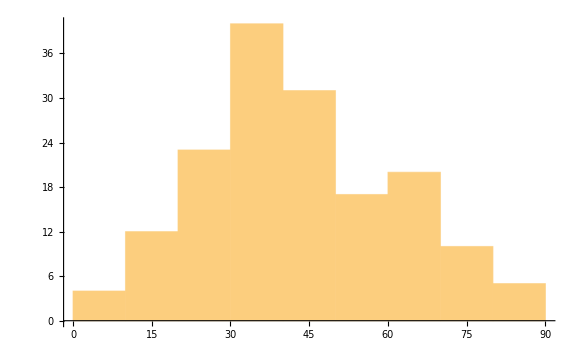

```mathematica
Select[ToExpression/@(OutputAgeEnglish/@FirstThreeLines//Flatten),NumberQ]//Histogram
```

#### Make Association

```mathematica
TitleList//Length
```

214

```mathematica
AllLines[[3]]
```

{                                    חולה 281 - 17/03/2020, 10:00                                ,החולה אישה בשנות השלושים לחייה מבית שמש. מגע של חולה מאומת.,מקומות חשיפה,5.3: 8:00-13:00 בית הספר עירוני ה' אבני החושן 57 במודיעין.,המגעים הקרובים של החולה כבר אותרו ומתודרכים באופן פרטני.}

```mathematica
SortBy[Table[StringDelete[ToString[#],{"{","}"}]&/@Join[{TitleList[[k,1]],DateString[TitleList[[k,2]]]},{OutputRegionEnglish[FirstThreeLines[[k]]],OutputGenderEnglish[FirstThreeLines[[k]]],OutputAgeEnglish[FirstThreeLines[[k]]]}],{k,Length[TitleList]}],#[[2]]&]//Length
```

214

```mathematica
Export["GenderAge1.xlsx",SortBy[Table[StringDelete[ToString[#],{"{","}"}]&/@Join[{TitleList[[k,1]],DateString[TitleList[[k,2]]]},{OutputRegionEnglish[FirstThreeLines[[k]]],OutputGenderEnglish[FirstThreeLines[[k]]],OutputAgeEnglish[FirstThreeLines[[k]]]}],{k,Length[TitleList]}],#[[2]]&],"XLSX"]
```

GenderAge1.xlsx

```mathematica
TitleList[[1,1]]//ToString//StringDelete[ToString[#],{"{","}"}]&
```

286